```mathematica
MatrixRank[Map[CoefficientList[First[#],x]&,Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5FakeAtomKeys}]//Tally//Sort]]
```

5

```mathematica
Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5FakeAtomKeys}]//Tally//Sort
```

{{x^5,1},{24 x-50 x^2+35 x^3-10 x^4+x^5,1},{-6 x^2+11 x^3-6 x^4+x^5,5},{-2 x^2+5 x^3-4 x^4+x^5,10},{2 x^3-3 x^4+x^5,10},{x^3-2 x^4+x^5,15},{-x^4+x^5,10}}

```mathematica
polys=Map[First,Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5FakeAtomKeys}]//Tally//Sort];
```

```mathematica
GroebnerBasis[polys,{x}]
```

{x}

```mathematica
Table[
With[{x1={0,0,0,0,0,1},x2={0,0,0,0,-1,1},x3={0,0,0,2,-3,1},x4={0,0,-6,11,-6,1},x5={0,24,-50,35,-10,1}},
Solve[PadLeft[CoefficientList[p,x],0]== a x1+b x2+c x3+d x4+e x5,{a,b,c,d,e}]
],
{p,polys}
]
```

{{},{},{},{},{},{},{}}

```mathematica
Table[
Indexed[x,n]==CoefficientList[Total[Table[StirlingS1[n,k]x^(5-n+k),{k,1,n}]],x],
{n,1,5}
]
```

{x1=={0,0,0,0,0,1},x2=={0,0,0,0,-1,1},x3=={0,0,0,2,-3,1},x4=={0,0,-6,11,-6,1},x5=={0,24,-50,35,-10,1}}

```mathematica
Map[CoefficientList[First[#],x]&,Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5FakeAtomKeys}]//Tally//Sort]
```

{{0,0,0,0,0,1},{0,24,-50,35,-10,1},{0,0,-6,11,-6,1},{0,0,-2,5,-4,1},{0,0,0,2,-3,1},{0,0,0,1,-2,1},{0,0,0,0,-1,1}}

```mathematica
IsSub[large_,small_]:=Block[{indices={},index,result=True,i,j,first,buck,temp, taken={}},
(*Print["large ", large];
Print["small ", small];*)
indices=Table[
Table[
temp=Position[large,s];
If[Length[temp]≠0,
index=temp[[1,1]]
,
(*Print[temp, " -- ", large , " --- ",s];*)
result=False;
index=-1
]
,
{s,bucket}
]
,{bucket,small}
];
(*Print[indices, "  " , result];*)
If[result,
If[Length[Tally[indices]]≠Length[small],
(*Print["tally problem ", indices];*)
result=False
,
For[i=1,i<=Length[indices],i++,
buck=indices[[i]];
If[Length[buck]==0,
(*Print["problem ", indices,  " -- NOT FOUND ",i];*)
result=False
,
first=buck[[1]];
If[MemberQ[taken,first],
result=False,
taken=Append[taken,first]
];
For[j=2,j<=Length[buck],j++,
(*Print["problem ", indices,  " ----- ",i, " ", j];*)
If[buck[[j]]≠first,
result=False
]
]
]
]
]
];
result
]
```

```mathematica
IsGood[sets_]:=Fold[Or,Table[IsSub[sets,allGraphs5[k,"vertexsets"]] ,{k,{alfa1Key,(*beta1Key,gamma1Key,delta1Key,epsilon1Key,*)quad1Key,quad2Key(*,quad3Key,quad4Key,quad5Key*)}}]]
```

```mathematica
ColorForSets[sets_]:=Block[{},
If[IsSub[sets,allGraphs5[alfa1Key,"vertexsets"]],Return[Red]];
If[IsSub[sets,allGraphs5[beta1Key,"vertexsets"]],Return[Blue]];
If[IsSub[sets,allGraphs5[gamma1Key,"vertexsets"]],Return[Green]];
If[IsSub[sets,allGraphs5[delta1Key,"vertexsets"]],Return[Darker[Yellow]]];
If[IsSub[sets,allGraphs5[epsilon1Key,"vertexsets"]],Return[Purple]];
Black
]
```

```mathematica
ColorForLargeSets[sets_]:=Block[{},
If[IsSub[sets,allGraphs5[quad1Key,"vertexsets"]],Return[Underlined]];
If[IsSub[sets,allGraphs5[quad2Key,"vertexsets"]],Return[Underlined]];
If[IsSub[sets,allGraphs5[quad3Key,"vertexsets"]],Return[Underlined]];
If[IsSub[sets,allGraphs5[quad4Key,"vertexsets"]],Return[Underlined]];
If[IsSub[sets,allGraphs5[quad5Key,"vertexsets"]],Return[Underlined]];
"Text"
]
```

```mathematica
IsAnyRefinement[set_,element_]:=Fold[Or,Table[IsRefinement[element,SymbolToSets[k]],{k,set}]]
```

```mathematica
SplitBlocksOne[sets_]:=Block[{result={},i,k,bucket,parts,new,startSets},
If[!ListQ[sets],
startSets=SymbolToSets[sets],
startSets=sets
];
For[i=1,i≤Length[startSets],i++,
bucket=startSets⟦i⟧;
parts=KSetPartitions[bucket,2];
(*Print[parts];*)
For[k=1,k≤Length[parts],k++,
new=startSets;
(*Print[" new before drop ",new, " to be dropped is ",i];*)
new=Drop[new,{i}];
(*Print[" new after drop ",new, " to be dropped is ",i];
Print[new->parts⟦k⟧];*)
new=Join[new,parts⟦k⟧];
new=Sort[Map[Sort[#]&,new],#1[[1]]<#2[[1]]&];
(*Print["new  ",new];*)
result=Append[result,new]
]
];
result
]
```

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

```mathematica
SplitBlocksOne[k134x2x5x6]
```

{{{1},{2},{3,4},{5},{6}},{{1,3},{2},{4},{5},{6}},{{1,4},{2},{3},{5},{6}}}

```mathematica
SplitBlocksOne[allGraphs5[alfa1Key,"vertexsets"]]
```

{{{1},{2,4},{3},{5}},{{1,3},{2},{4},{5}}}

## Now we test whether the incoming for the alfas are an intersection of the incomings of the quads

```mathematica
Table[ShowGraph5Least[k] ,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
```

{-Graphics-361660,-Graphics-317380,-Graphics-296080,-Graphics-361120,-Graphics-317140,-Graphics-360850,-Graphics-296050,-Graphics-295270,-Graphics-317110,-Graphics-295510}

```mathematica
theSize=7;
```

```mathematica
all=With[
{n=theSize},
DeleteDuplicates[Flatten[Table[Map[SetsToSymbol[#]&, Select[KSetPartitions[Range[n],4],IsSub[#,allGraphs5[k,"vertexsets"]]&]],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]]
];Length[all]
```

80

```mathematica
all6=With[
{n=theSize},
Map[SetsToSymbol,Sort[DeleteDuplicates[Flatten[Table[SplitBlocksOne[k],{k,all}],1]]]]
];Length[all6]
```

70

```mathematica
some=With[
{n=theSize},
DeleteDuplicates[Flatten[Table[Map[SetsToSymbol[#]&, Select[KSetPartitions[Range[n],4],IsSub[#,allGraphs5[k,"vertexsets"]]&]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]]
];Length[some]
```

35

```mathematica
some
```

{v13x24x5x67,v13x24x56x7,v13x24x57x6,v13x246x5x7,v13x247x5x6,v136x24x5x7,v137x24x5x6,v14x25x3x67,v14x256x3x7,v14x257x3x6,v146x25x3x7,v147x25x3x6,v14x25x36x7,v14x25x37x6,v1x24x35x67,v1x24x356x7,v1x24x357x6,v1x246x35x7,v1x247x35x6,v16x24x35x7,v17x24x35x6,v13x25x4x67,v13x256x4x7,v13x257x4x6,v13x25x46x7,v13x25x47x6,v136x25x4x7,v137x25x4x6,v14x2x35x67,v14x2x356x7,v14x2x357x6,v146x2x35x7,v147x2x35x6,v14x26x35x7,v14x27x35x6}

```mathematica
some6=With[
{n=theSize},
Map[SetsToSymbol,Sort[DeleteDuplicates[Flatten[Table[SplitBlocksOne[k],{k,some}],1]]]]
];Length[some6]
```

50

```mathematica
some6
```

{v1x2x35x4x67,v1x2x35x46x7,v1x2x35x47x6,v1x2x356x4x7,v1x2x357x4x6,v1x24x3x5x67,v1x24x3x56x7,v1x24x3x57x6,v1x24x35x6x7,v1x24x36x5x7,v1x24x37x5x6,v1x25x3x4x67,v1x25x3x46x7,v1x25x3x47x6,v1x25x36x4x7,v1x25x37x4x6,v1x26x35x4x7,v1x27x35x4x6,v1x246x3x5x7,v1x247x3x5x6,v1x256x3x4x7,v1x257x3x4x6,v13x2x4x5x67,v13x2x4x56x7,v13x2x4x57x6,v13x2x46x5x7,v13x2x47x5x6,v13x24x5x6x7,v13x25x4x6x7,v13x26x4x5x7,v13x27x4x5x6,v14x2x3x5x67,v14x2x3x56x7,v14x2x3x57x6,v14x2x35x6x7,v14x2x36x5x7,v14x2x37x5x6,v14x25x3x6x7,v14x26x3x5x7,v14x27x3x5x6,v16x2x35x4x7,v16x24x3x5x7,v16x25x3x4x7,v17x2x35x4x6,v17x24x3x5x6,v17x25x3x4x6,v136x2x4x5x7,v137x2x4x5x6,v146x2x3x5x7,v147x2x3x5x6}

```mathematica
Intersection[all6,some6]//Length
```

45

```mathematica
Table[SetsToSymbol[allGraphs5[k,"vertexsets"]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
SetDifference[some6,all6]
```

{v1x24x35x6x7,v13x24x5x6x7,v13x25x4x6x7,v14x2x35x6x7,v14x25x3x6x7}

```mathematica
SetDifference[some6,all6]//Length
```

5

```mathematica
Length[VertexList[Graph[plantri[[8]]]]]
```

17

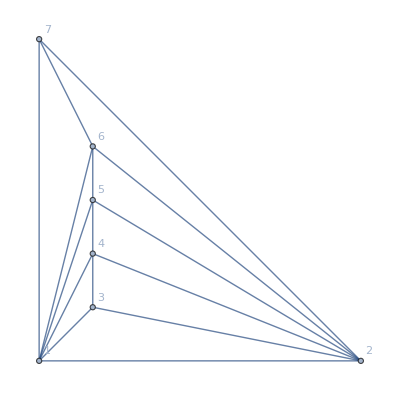
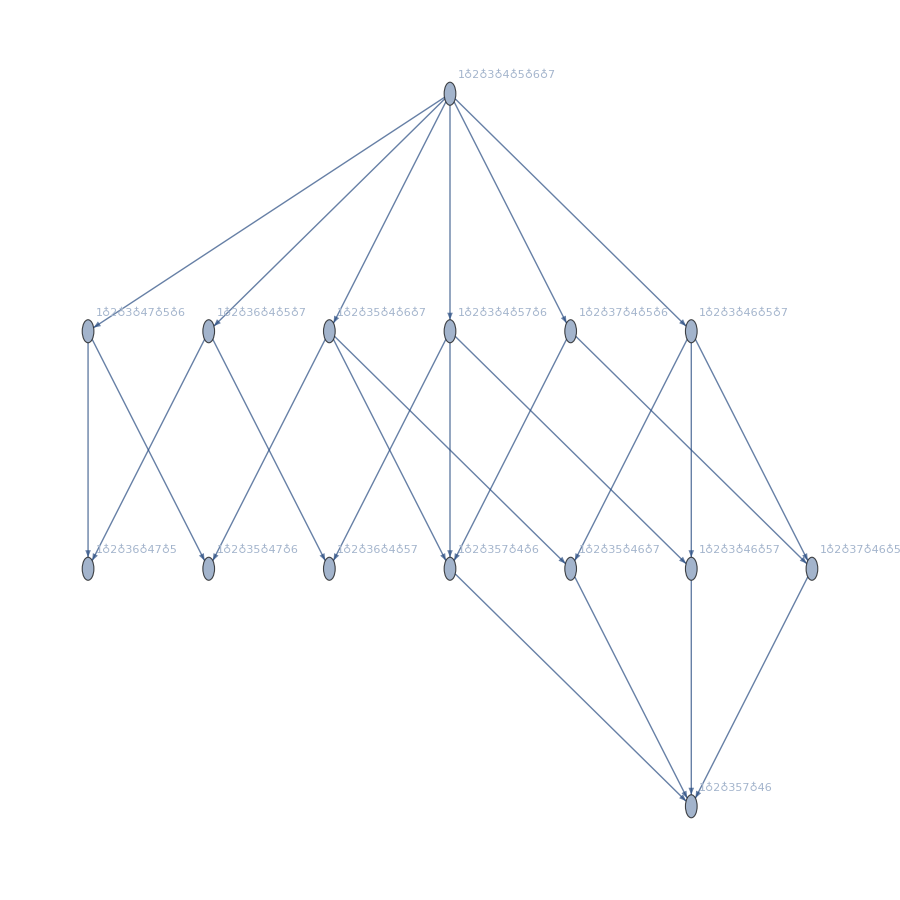

```mathematica
With[{g=MinimalGraph[6]},
{g,FormulaGraph[FindFullFormula[ g]]}]
```

## Now paint the graph

```mathematica
Rotate[Graph[EdgeList[FormulaGraph[Join[some,some6,all,all6]]],VertexStyle->Join[
Table[k-> Blue,{k,Join[some,some6]}],
Table[k-> Red,{k,SetDifference[Join[some,some6,all,all6],Join[some,some6]]}]
],
VertexLabels->Table[k->Rotate [ SymbolToLabel[k],-Pi/2],{k,Join[some,some6,all,all6]}],
VertexLabelStyle->Join[
Table[k-> Underlined,{k,Join[all,all6]}]
],
VertexSize->{1,1/4}/20,
EdgeShapeFunction->GraphElementData[{"FilledArcArrow","ArrowSize"->.005}],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->{2000,500},
AspectRatio->1/4],Pi/2]
```

SymbolName::sym: Argument {{1},{2,4},{3},{5},{6}} at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[{{1},{2,4},{3},{5},{6}}],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[{{1},{2,4},{3},{5},{6}}],1],x].

Riffle::list: List expected at position 1 in Riffle[StringSplit[StringDrop[SymbolName[{{1},{2,4},{3},{5},{6}}],1],x],♁].

SymbolName::sym: Argument {{1,3},{2},{4},{5},{6}} at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[{{1,3},{2},{4},{5},{6}}],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[{{1,3},{2},{4},{5},{6}}],1],x].

Riffle::list: List expected at position 1 in Riffle[StringSplit[StringDrop[SymbolName[{{1,3},{2},{4},{5},{6}}],1],x],♁].

SymbolName::sym: Argument {{1},{2},{3},{4},{5,6}} at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[{{1},{2},{3},{4},{5,6}}],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[{{1},{2},{3},{4},{5,6}}],1],x].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[StringSplit[StringDrop[SymbolName[{{1},{2},{3},{4},{5,6}}],1],x],♁].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

-Graphics-

## Showing the partitions

```mathematica
Doit[n_]:=Block[{result={}},
Table[
Table[
If[IsRefinement[four,five] && IsGood[four],
result=AppendTo[result,Style[SymbolToLabel[SetsToSymbol[ five]]->SymbolToLabel[SetsToSymbol[four]],ColorForSets[four],ColorForLargeSets[four]]]
]
,{five,KSetPartitions[Range[n],5]}
]
,{four,KSetPartitions[Range[n],4]}
];
result
]; Multicolumn[Doit[6]//Sort,5,Spacings -> {3,1}]
```

1♁2♁3♁4♁56→1♁24♁3♁56 | 1♁2♁36♁4♁5→1♁24♁36♁5 | 1♁24♁3♁5♁6→1♁246♁3♁5 | 1♁26♁3♁4♁5→13♁26♁4♁5 | 13♁2♁4♁5♁6→13♁26♁4♁5
1♁2♁3♁4♁56→13♁2♁4♁56 | 1♁2♁36♁4♁5→136♁2♁4♁5 | 1♁24♁3♁5♁6→13♁24♁5♁6 | 13♁2♁4♁5♁6→13♁2♁4♁56 | 13♁2♁4♁5♁6→136♁2♁4♁5
1♁2♁3♁46♁5→1♁246♁3♁5 | 1♁24♁3♁5♁6→1♁24♁3♁56 | 1♁24♁3♁5♁6→16♁24♁3♁5 | 13♁2♁4♁5♁6→13♁2♁46♁5 | 16♁2♁3♁4♁5→136♁2♁4♁5
1♁2♁3♁46♁5→13♁2♁46♁5 | 1♁24♁3♁5♁6→1♁24♁36♁5 | 1♁26♁3♁4♁5→1♁246♁3♁5 | 13♁2♁4♁5♁6→13♁24♁5♁6 | 16♁2♁3♁4♁5→16♁24♁3♁5

```mathematica
Map[SetsToSymbol2[#]&,KSetPartitions[Range[6],4]]
```

{v1x2x3x456,v1x2x34x56,v1x2x356x4,v1x2x345x6,v1x2x36x45,v1x2x346x5,v1x2x35x46,v1x23x4x56,v1x24x3x56,v1x256x3x4,v1x23x45x6,v1x245x3x6,v1x26x3x45,v1x23x46x5,v1x246x3x5,v1x25x3x46,v1x234x5x6,v1x25x34x6,v1x26x34x5,v1x235x4x6,v1x24x35x6,v1x26x35x4,v1x236x4x5,v1x24x36x5,v1x25x36x4,v12x3x4x56,v13x2x4x56,v14x2x3x56,v156x2x3x4,v12x3x45x6,v13x2x45x6,v145x2x3x6,v16x2x3x45,v12x3x46x5,v13x2x46x5,v146x2x3x5,v15x2x3x46,v12x34x5x6,v134x2x5x6,v15x2x34x6,v16x2x34x5,v12x35x4x6,v135x2x4x6,v14x2x35x6,v16x2x35x4,v12x36x4x5,v136x2x4x5,v14x2x36x5,v15x2x36x4,v123x4x5x6,v14x23x5x6,v15x23x4x6,v16x23x4x5,v124x3x5x6,v13x24x5x6,v15x24x3x6,v16x24x3x5,v125x3x4x6,v13x25x4x6,v14x25x3x6,v16x25x3x4,v126x3x4x5,v13x26x4x5,v14x26x3x5,v15x26x3x4}

```mathematica
Map[CoefficientList[First[#],x]&,Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5FakeAtomKeys}]//Tally//Sort]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1
0 | 24 | -50 | 35 | -10 | 1
0 | 0 | -6 | 11 | -6 | 1
0 | 0 | -2 | 5 | -4 | 1
0 | 0 | 0 | 2 | -3 | 1
0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | -1 | 1)

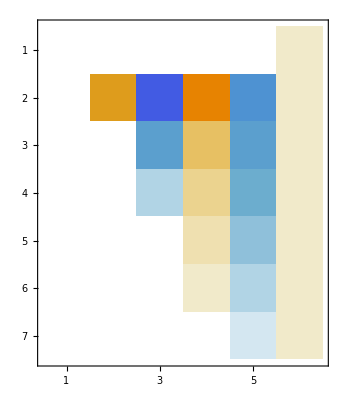

```mathematica
MatrixPlot[Map[CoefficientList[First[#],x]&,Table[ChromaticPolynomial[allGraphs5[k,"graph"],x],{k,allGraphs5FakeAtomKeys}]//Tally//Sort]]
```